# Information Theory of Complex Systems: Cellular Automaton

CellularAutomatonpaclet:ref/CellularAutomaton[rule,init,t]
generates a list representing the evolution of the cellular automaton with the specified rule from initial condition init for t steps.

```mathematica
CellularAutomaton[1,{0,0,0,1,0,0,0},2]
```

{{0,0,0,1,0,0,0},{1,1,0,0,0,1,1},{0,0,0,1,0,0,0}}

To plot it use ArrayPlot

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},100]]
```

-Graphics-

## Class I: R32, Cellular automata which rapidly converge to a uniform state.

```mathematica
initialConditions = RandomInteger[1,{1,1000}];
ArrayPlot[CellularAutomaton[32,initialConditions[[1]],10], ImageSize -> Full]
```

-Graphics-

## Class II: R4, Cellular automata which rapidly converge to a repetitive or stable state.

```mathematica
initialConditions = RandomInteger[1,{1,1000}];
ArrayPlot[CellularAutomaton[4,initialConditions[[1]],600], ImageSize -> Full]
```

-Graphics-

## Class II: R22, Cellular automata which appear to remain in a random state.

```mathematica
initialConditions = RandomInteger[1,{1,1000}];
ArrayPlot[CellularAutomaton[22,initialConditions[[1]],1000], ImageSize -> Full]
```

-Graphics-

## Class IV: R110, Cellular automata which form areas of repetitive or stable states, but also form structures that interact with each other in complicated ways. Rule 110 has been shown to be capable of universal computation.

```mathematica
initialConditions = RandomInteger[1,{1,1000}];
ArrayPlot[CellularAutomaton[110,initialConditions[[1]],1000], ImageSize -> Full]
```

-Graphics-

Generate an icon for a cellular automaton rule:

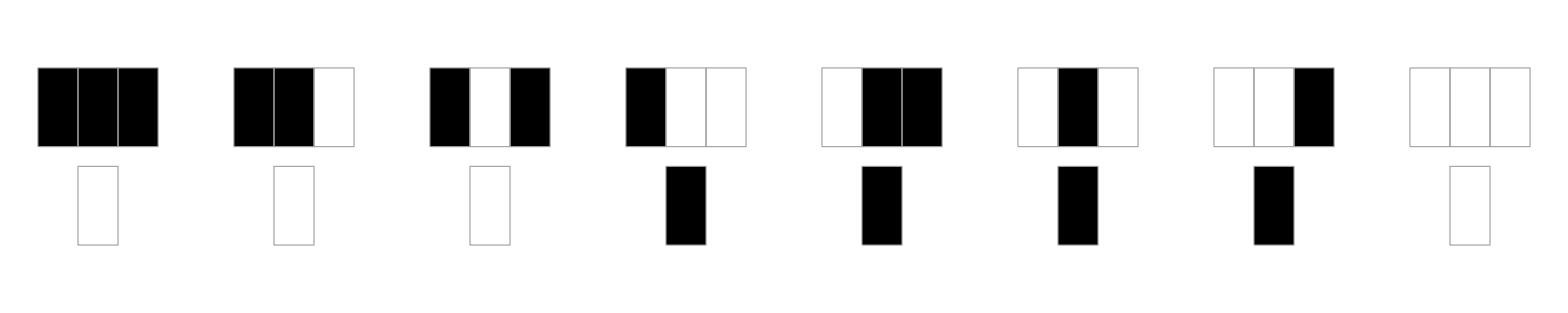

```mathematica
RulePlot[CellularAutomaton[30]]
```

## Game of life

```mathematica
gameOfLife = {224, {2, {{2, 2, 2}, {2, 1, 2}, {2, 2, 2}}}, {1, 1}};
board = RandomInteger[1, {50, 50}];
Dynamic[ArrayPlot[
  board = Last[CellularAutomaton[gameOfLife, board, {{0, 1}}]]]];
```

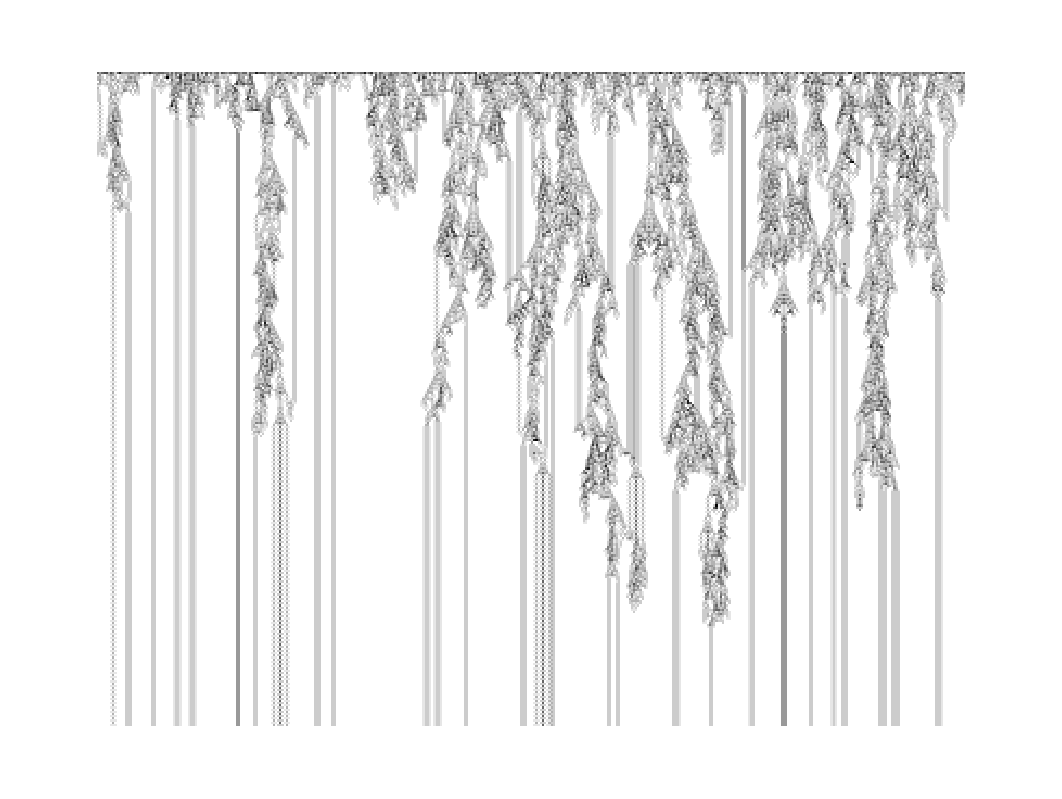

```mathematica
ArrayPlot[
 Mean /@ CellularAutomaton[gameOfLife, RandomInteger[1, {10, 400}], 
   300]]
```